## Set 6: Numerical Computations with Mathematica

First, we integrate the equations of motion without drag.

```mathematica
EqNoDrag={X''[T]==0,Y''[T]==-g}
```

{X''(T)==0,Y''(T)==-g}

```mathematica
Init={X[0]==0,Y[0]==0,X'[0]==V Cos[θ], Y'[0]==V Sin[θ]}
```

{X(0)==0,Y(0)==0,X'(0)==V cos(θ),Y'(0)==V sin(θ)}

```mathematica
NoDragSystem=Join[EqNoDrag,Init]
```

{X''(T)==0,Y''(T)==-g,X(0)==0,Y(0)==0,X'(0)==V cos(θ),Y'(0)==V sin(θ)}

```mathematica
NoDragSolution=Simplify[DSolve[NoDragSystem,{X[T],Y[T]},T]]
```

{{X(T)→T V cos(θ),Y(T)→T V sin(θ)-(g T^2)/2}}

```mathematica
x[t_]:=(X[T]/.NoDragSolution[[1]])/.T->t
```

```mathematica
y[t_]:=(Y[T]/.NoDragSolution[[1]])/.T->t
```

We derive the range of the projectile and show that it is maximized with at 45-degree firing angle.

```mathematica
NoDragTimeAtGround=Solve[y[t]==0,t]
```

{{t→0},{t→(2 V sin(θ))/g}}

```mathematica
NoDragXPositionsAtGround=x[t]/.NoDragTimeAtGround
```

{0,(2 V^2 sin(θ) cos(θ))/g}

```mathematica
NoDragXRange=NoDragXPositionsAtGround[[2]]-NoDragXPositionsAtGround[[1]]
```

(2 V^2 sin(θ) cos(θ))/g

```mathematica
Solve[(D[NoDragXRange, θ])==0,θ]
```

{{θ→ConditionalExpression[2 π c_1-(3 π)/4,c_1∈ℤ]},{θ→ConditionalExpression[2 π c_1-π/4,c_1∈ℤ]},{θ→ConditionalExpression[2 π c_1+π/4,c_1∈ℤ]},{θ→ConditionalExpression[2 π c_1+(3 π)/4,c_1∈ℤ]}}

These solutions all correspond to 45 degrees. We want to reach PCC, which is 1000 m away. With the optimal firing angle, we find the required velocity.

```mathematica
StandardFiring={θ->π/4}
```

{θ→π/4}

```mathematica
PhysicalConditions={g->9.81}
```

{g→9.81}

```mathematica
VelocityNoDrag=(NSolve[NoDragXRange==1000,V]/.Join[StandardFiring,PhysicalConditions])[[2]]
```

{V→99.0454}

We also show the optimal performance of the 45-degree angle visually.

```mathematica
Nx[t_,θ_]:=x[t]/.Join[PhysicalConditions,VelocityNoDrag]
```

```mathematica
Ny[t_,θ_]:=y[t]/.Join[PhysicalConditions,VelocityNoDrag]
```

```mathematica
ToRad[Θ_]:=(2π)/360*Θ
```

```mathematica
FiringAngles={ToRad[15],ToRad[30],ToRad[45],ToRad[60],ToRad[75]}
```

{π/12,π/6,π/4,π/3,(5 π)/12}

```mathematica
Traj=Transpose[{Nx[t,θ],Ny[t,θ]}/.θ->FiringAngles]
```

(95.6706 t | 25.6348 t-4.905 t^2
85.7759 t | 49.5227 t-4.905 t^2
70.0357 t | 70.0357 t-4.905 t^2
49.5227 t | 85.7759 t-4.905 t^2
25.6348 t | 95.6706 t-4.905 t^2)

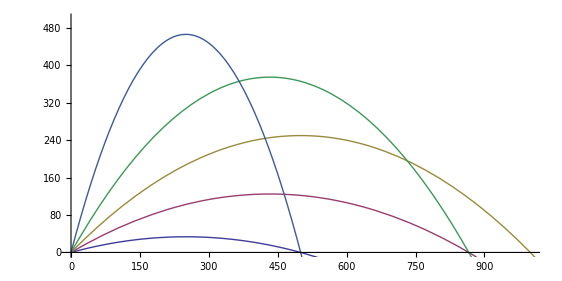

```mathematica
ParametricPlot[Traj,{t,0,20},PlotRange->{{0, 1000},{0,500}}]
```

Clearly, the 45-degree firing angle maximizes the projectile’s range. We now include the drag force in our equations of motion and generate a more accurate solution.

```mathematica
FDrag=-1/2 ρ r^2 v^2
```

-1/2 ρ r^2 ((X'(T))^2+(Y'(T))^2)

```mathematica
v=√((X'[T])^2+(Y'[T])^2)
```

√((X'(T))^2+(Y'(T))^2)

```mathematica
EqDrag={X''[T]==FDrag/m*X'[T]/v,Y''[T]==-g+(FDrag/m*Y'[T]/v)}
```

{X''(T)==-(ρ r^2 X'(T) √((X'(T))^2+(Y'(T))^2))/(2 m),Y''(T)==-g-(ρ r^2 Y'(T) √((X'(T))^2+(Y'(T))^2))/(2 m)}

```mathematica
Init={X[0]==0,Y[0]==0,X'[0]==V Cos[θ], Y'[0]==V Sin[θ]}
```

{X(0)==0,Y(0)==0,X'(0)==V cos(θ),Y'(0)==V sin(θ)}

```mathematica
DragSystem=Join[EqDrag,Init]
```

{X''(T)==-(ρ r^2 X'(T) √((X'(T))^2+(Y'(T))^2))/(2 m),Y''(T)==-g-(ρ r^2 Y'(T) √((X'(T))^2+(Y'(T))^2))/(2 m),X(0)==0,Y(0)==0,X'(0)==V cos(θ),Y'(0)==V sin(θ)}

```mathematica
DragConditions={g->9.81,ρ->1.3,r->0.05,m->0.5}
```

{g→9.81,ρ→1.3,r→0.05,m→0.5}

```mathematica
DragSolution[argV_,argθ_]:=NDSolve[(DragSystem/.Join[DragConditions,{V->argV,θ->argθ}]),{X[T],Y[T]},{T,0,1000}]
```

```mathematica
x[V_,θ_,t_]:=(X[T]/.(DragSolution[V,θ])[[1]])/.T->t
```

```mathematica
y[V_,θ_,t_]:=(Y[T]/.(DragSolution[V,θ])[[1]])/.T->t
```

We compute the time of impact with a starting guess equivalent to the time of impact in the non-drag case.

```mathematica
DragImpactTime[V_,θ_]:=FindRoot[y[V,θ,t]==0,{t,(2V Sin[θ])/9.81}]
```

```mathematica
DragXRange[V_,θ_]:=x[V,θ,(t/.DragImpactTime[V,θ])]
```

```mathematica
DragXRange[(V/.VelocityNoDrag),(θ/.StandardFiring)]
```

333.33

Thus, with the same initial speed and 45-degree angle that we found optimal in the no-drag case, the projectile travels one-third of the desired distance. We now want to find the optimal firing conditions with drag - i.e. the firing angle that requires the least initial speed.

To do this, we first define a function that, given a firing angle, finds the minimum velocity required to travel a given range by iterating through possible velocities.

```mathematica
DragMinVelocityForRange[θ_,D_]:=Module[
{V},
V=0;
While[DragXRange[V,θ]<D,
V=V+500];
V = V-500;
While[DragXRange[V,θ]<D,
V=V+100];
V=V-100;
While[DragXRange[V,θ]<D,
V=V+10];
V=V-10;
While[DragXRange[V,θ]<D,
V=V+1];
V=V-1;
While[DragXRange[V,θ]<D,
V=V+0.1];
V=V-1;
V]
```

```mathematica
DragMinVelocityForRange[π/4,1000]
```

1320.9

With a 45-degree firing angle, we would need to fire the projectile at a whopping 1320.9 m/s to reach PCC. We now iterate through various firing angles, find the minimum velocity required for each angle, find the lowest among these minimum velocities, and return the firing angle associated with that velocity - the optimum firing angle.

```mathematica
DragOptimalAngle[D_]:=Module[
{θ},
θ=ToRad[1];
While[DragMinVelocityForRange[θ+ToRad[10],D]<DragMinVelocityForRange[θ,D],
θ=θ+ToRad[10]];
While[DragMinVelocityForRange[θ+ToRad[1],D]<DragMinVelocityForRange[θ,D],
θ=θ+ToRad[1]];
θ]
```

```mathematica
DragOptimalAngle[1000]
```

(2 π)/15

```mathematica
ToDeg[θ_]:=360/(2π)*θ
```

```mathematica
ToDeg[2π/15]
```

24

Thus, we find that a 24-degree angle is optimal. Figure 2 below shows the trajectories for various firing angles, with the initial velocities adjusted to be the minimum velocity required to travel 1000 m.

```mathematica
DragFiringAngles={ToRad[15],ToRad[24],ToRad[30],ToRad[40],ToRad[50]}
```

{π/12,(2 π)/15,π/6,(2 π)/9,(5 π)/18}

```mathematica
DragTraj =Table[{x[(DragMinVelocityForRange[θ,1000]),θ,t],y[(DragMinVelocityForRange[θ,1000]),θ,t]},{θ,DragFiringAngles}]
```

(InterpolatingFunction[(0. | 1000.),<>](t) | InterpolatingFunction[(0. | 1000.),<>](t)
InterpolatingFunction[(0. | 1000.),<>](t) | InterpolatingFunction[(0. | 1000.),<>](t)
InterpolatingFunction[(0. | 1000.),<>](t) | InterpolatingFunction[(0. | 1000.),<>](t)
InterpolatingFunction[(0. | 1000.),<>](t) | InterpolatingFunction[(0. | 1000.),<>](t)
InterpolatingFunction[(0. | 1000.),<>](t) | InterpolatingFunction[(0. | 1000.),<>](t))

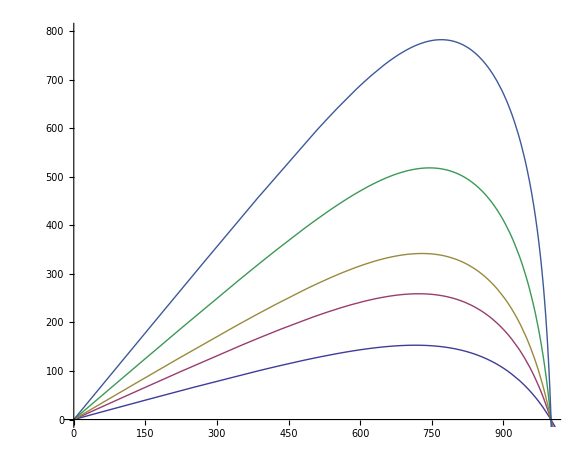

```mathematica
ParametricPlot[DragTraj,{t,0,100},PlotRange->{{0, 1000},{0,800}}]
```